#### Numerical Methods

```mathematica
CheckIntensity[Rays_]:=Module[{i,Intnum,check,power,j},
Intnum=Rays[[Length[Rays],1]];
i=1;
While[Rays[[i,1]]==0,
i=i+1;
];
check=Intnum*i;
power=0;
For[j=1,j≤Length[Rays],j++,
power=power+Rays[[j,4]];
];
If[Abs[power-check]<1,
Return[True],
Return[False];
];
];
```

```mathematica
Newton[F_,DF_,x0_,eps_] := Module[{x, deltax,val},
x = x0;
val=1;
While[Abs[val] ≥ eps,
deltax = -F[x]/DF[x];
x = x + deltax;
val = deltax;
];
Return[x];
];
BisectWhile[F_, xl_, xr_, eps_]:= Module[{val, vam, xm,xll, retval,count},
xm = .5(xl + xr);
xll=xl;
count=0;
While[
Abs[F[xm]]>eps,
count=count+1;
val = F[xll];
vam = F[xm];
If[val vam < 0,
xm= .5(xll + xm);
,
xm=xm+0.5(xm-xll);
xll=xll+(2/3.)(xm-xll);
];
If[count==35,
Return[0];
];
];
retval=xm;
Return[retval];
];
```

```mathematica
RobbyRoot[F_,xl_,xr_]:=Module[{s0,a},
s0=BisectWhile[F,xl,xr,.1];
Return[Newton[F,F',s0,10^-6]];
];
```

```mathematica
RootFind[F_]:=Module[{a,i},
a=s/.NSolve[F[s]==0,s,Reals];
For[i=1,i≤Length[a],i++,
If[a[[i]]>0.005,
Return[a[[i]]];
];
];
];
```

#### Fresnel Equations

```mathematica
R[Ray_,normal_,n1_,n2_]:=Module[{θi,θc},
If[n1>n2,
θc=ArcSin[n2/n1];
θi=ArcCos[-normal.Ray[[3]]];
If[θi≥θc,
Return[1];
];
];
Return[((n1*(-Ray[[3]].normal)-n2*√(1-(n1/n2)^2(1-(-Ray[[3]].normal)^2)))/(n1*(-Ray[[3]].normal)+n2*√(1-(n1/n2)^2(1-(-Ray[[3]].normal)^2))))^2];
];
T[R_]:=1-R;
```

```mathematica
RR[ReflectedRay_,normal_,n1_,n2_]:=((n1(-normal.ReflectedRay[[3]])-n2 √(1-n1/n2(√(1-(-normal.ReflectedRay[[3]])^2))))/(n1(-normal.ReflectedRay[[3]])+n2 √(1-n1/n2(√(1-(-normal.ReflectedRay[[3]])^2)))))^2;
```

#### Ray Initialization

```mathematica
Rays[n_]:=Table[{0,0,{1,0},1,False},{p,1,n}];
(* {raynum,position,direction,intensity,Flip n's?} *)

Raypositions[n_,Leng_,xstart_,α_]:=Module[{i,new},
new=Rays[n];
For[i=0,i<Length[new],i=i+1,
new[[i+1,2]]={-xstart,-Leng/2+i*Leng/(Length[new]-1)};
new[[i+1,3]]=N[RotationMatrix[α].new[[i+1,3]]];
new[[i+1,2]]=N[RotationMatrix[α].new[[i+1,2]]];
];
Return[new];
];
```

```mathematica
RayShooting[n_,α_,F_]:=Module[{Raylist,Vector,xdir,ydir,Δx,tot,xpos,ypos,k,j,Firsthit,Endhit,xprop,yprop,FF,intersect,i,p},
Raylist=Raypositions[n,3,2,α];
Vector=Normalize[{-2 Cos[α],-2 Sin[α]}-{-2 Cos[α]-Sin[α],-2 Sin[α]+Cos[α]}];
xdir=Table[Raylist[[i,3,1]],{i,1,Length[Raylist]}];
ydir=Table[Raylist[[i,3,2]],{i,1,Length[Raylist]}];
xpos=Table[Raylist[[i,2,1]],{i,1,Length[Raylist]}];
ypos=Table[Raylist[[i,2,2]],{i,1,Length[Raylist]}];
xprop[x_]:=Table[xpos[[i]]+xdir[[i]]*x,{i,1,Length[Raylist]}];
yprop[x_]:=Table[ypos[[i]]+ydir[[i]]*x,{i,1,Length[Raylist]}];
FF[x_]:=Table[F[xprop[x][[i]],yprop[x][[i]]],{i,1,Length[Raylist]}];
intersect=Table[0,{i,1,Length[Raylist]}];

For[i=1,i≤Length[Raylist],i++,
p[x_]:=FF[x][[i]];
intersect[[i]]=BisectWhile[p,0,4,10^-8];
];
j=1;
k=n;
While[intersect[[j]]==0,
j=j+1;
];
While[intersect[[k]]==0,
k=k-1;
];
Firsthit=Raylist[[j,2]];
If[α≤π/2,
Firsthit=Firsthit-{.05,0};
];
Endhit=Raylist[[k,2]];
If[α≥3π/2,
Endhit=Endhit-{.05,0};
];
tot=Firsthit-Endhit;
Δx=(√(tot[[1]]^2+tot[[2]]^2))/(n-1);
For[i=1,i<=n,i++,
Raylist[[i,2]]=Firsthit-(i-1)*Δx*Vector;
Raylist[[i,4]]=(√(tot[[1]]^2+tot[[2]]^2))/3;
];
Return[Raylist];
];
```

```mathematica
RayShooting2[n_,α_]:=Module[{Q,a,Raylist,first,end,tot,magtot,Δx,i},
Raylist=Raypositions[n,3,2,α];
a={Cos[α+π/2],Sin[α+π/2]};
Q[x_,y_]:=-Cot[α](x+2 Cos[α]+Sin[α])-y+Cos[α]-2 Sin[α];

If[α>0&&α<π/2,
first=Propogate[{{0,a-{0,.01},-{Cos[α],Sin[α]},1,False}},Q][[1]];
end=Propogate[{{0,{0,-.99},-{Cos[α],Sin[α]},1,False}},Q][[1]];
];
If[α==π/2,
first={-.99,-2};
end={-.01,-2};
];
If[α==3π/2,
first={-.99,2};
end={-.01,2};
];
If[α>π/2&&α<π,
first=Propogate[{{0,a+{0,.01},-{Cos[α],Sin[α]},1,False}},Q][[1]];
end=Propogate[{{0,{0,.99},-{Cos[α],Sin[α]},1,False}},Q][[1]];
];

If[α==π,
Return[Raypositions[n,1.99,2,α]];
];
If[α==0||α==2π,
Return[Raypositions[n,1.99,2,α]];
];

If[α>π&&α<3π/2,
a={Cos[α-π/2],Sin[α-π/2]};
first=Propogate[{{0,a,-{Cos[α],Sin[α]},1,False}},Q][[1]];
end=Propogate[{{0,{0,-.99},-{Cos[α],Sin[α]},1,False}},Q][[1]];
];

If[α>3π/2&&α<2π,
a={Cos[α-π/2],Sin[α-π/2]};
first=Propogate[{{0,a,-{Cos[α],Sin[α]},1,False}},Q][[1]];
end=Propogate[{{0,{0,.99},-{Cos[α],Sin[α]},1,False}},Q][[1]];
];

tot=end-first;
magtot=√(tot[[1]]^2+tot[[2]]^2);
Δx=magtot/(n-1);

For[i=0,i<n,i++,
Raylist[[i+1,2]]=first+(i*Δx*tot/magtot);
If[α≤π/2||α≥3π/2,
Raylist[[i+1,4]]=(1+Cos[α])/2,
Raylist[[i+1,4]]=(1-Cos[α])/2;
];
];


Return[Raylist];
];
```

```mathematica
RayShooting3[n_,α_]:=Module[{Q,a,Raylist,first,end,tot,magtot,Δx,i},
Raylist=Raypositions[n,3,2,α];
a={Cos[α+π/2],Sin[α+π/2]};
Q[x_,y_]:=-Cot[α](x+2 Cos[α]+Sin[α])-y+Cos[α]-2 Sin[α];

If[α>0&&α<π/2,
first=Propogate[{{0,a-{0,.01},-{Cos[α],Sin[α]},1,False}},Q][[1]];
end=Propogate[{{0,{0,-.99},-{Cos[α],Sin[α]},1,False}},Q][[1]];
];
If[α==π/2,
first={-.99,-2};
end={-.01,-2};
];
If[α==3π/2,
first={-.99,2};
end={-.01,2};
];
If[α>π/2&&α<π,
first=Propogate[{{0,a+{0,.01},-{Cos[α],Sin[α]},1,False}},Q][[1]];
end=Propogate[{{0,{-.01,-.99},-{Cos[α],Sin[α]},1,False}},Q][[1]];
];

If[α==π,
Return[Raypositions[n,1.99,2,α]];
];
If[α==0||α==2π,
Return[Raypositions[n,1.99,2,α]];
];

If[α>π&&α<3π/2,
a={Cos[α-π/2],Sin[α-π/2]};
first=Propogate[{{0,a,-{Cos[α],Sin[α]},1,False}},Q][[1]];
end=Propogate[{{0,{-.01,.99},-{Cos[α],Sin[α]},1,False}},Q][[1]];
];

If[α>3π/2&&α<2π,
a={Cos[α-π/2],Sin[α-π/2]};
first=Propogate[{{0,a,-{Cos[α],Sin[α]},1,False}},Q][[1]];
end=Propogate[{{0,{0,.99},-{Cos[α],Sin[α]},1,False}},Q][[1]];
];

tot=end-first;
magtot=√(tot[[1]]^2+tot[[2]]^2);
Δx=magtot/(n-1);

For[i=0,i<n,i++,
Raylist[[i+1,2]]=first+(i*Δx*tot/magtot);
If[α≤π/2||α≥3π/2,
Raylist[[i+1,4]]=(1+Cos[α])/2,
Raylist[[i+1,4]]=(1+Cos[α])/2;
];
];


Return[Raylist];
];
```

```mathematica
Sin[α-π/2]
```

-Cos[α]

#### Find Ray Intersections

```mathematica
Propogate[Raylist_,F_]:=Module[{Intersection,xprop,DFX,DFY,ypos,xpos,i,p,pp,xdir,ydir,FFF,yprop,FF,intersect},
xdir=Table[Raylist[[i,3,1]],{i,1,Length[Raylist]}];
ydir=Table[Raylist[[i,3,2]],{i,1,Length[Raylist]}];

xpos=Table[Raylist[[i,2,1]],{i,1,Length[Raylist]}];
ypos=Table[Raylist[[i,2,2]],{i,1,Length[Raylist]}];

xprop[x_]:=Table[xpos[[i]]+xdir[[i]]*x,{i,1,Length[Raylist]}];
yprop[x_]:=Table[ypos[[i]]+ydir[[i]]*x,{i,1,Length[Raylist]}];

FF[x_]:=Table[F[xprop[x][[i]],yprop[x][[i]]],{i,1,Length[Raylist]}];
intersect=Table[0,{i,1,Length[Raylist]}];
For[i=1,i≤Length[Raylist],i++,
p[x_]:=FF[x][[i]];
pp[x_]:=D[p,x];
intersect[[i]]=RootFind[p];
];



Intersection=Table[{xprop[intersect[[i]]][[i]],yprop[intersect[[i]]][[i]]},{i,1,Length[intersect]}];

Return[Intersection];
];
```

```mathematica
Sstop[Raylist_,F_]:=Module[{Intersection,xprop,DFX,DFY,ypos,xpos,i,p,pp,xdir,ydir,FFF,yprop,FF,intersect},
xdir=Table[Raylist[[i,3,1]],{i,1,Length[Raylist]}];
ydir=Table[Raylist[[i,3,2]],{i,1,Length[Raylist]}];

xpos=Table[Raylist[[i,2,1]],{i,1,Length[Raylist]}];
ypos=Table[Raylist[[i,2,2]],{i,1,Length[Raylist]}];

xprop[x_]:=Table[xpos[[i]]+xdir[[i]]*x,{i,1,Length[Raylist]}];
yprop[x_]:=Table[ypos[[i]]+ydir[[i]]*x,{i,1,Length[Raylist]}];

FF[x_]:=Table[F[xprop[x][[i]],yprop[x][[i]]],{i,1,Length[Raylist]}];
intersect=Table[0,{i,1,Length[Raylist]}];
For[i=1,i≤Length[Raylist],i++,
p[x_]:=FF[x][[i]];
pp[x_]:=D[p,x];
intersect[[i]]=RootFind[p];
];
Return[intersect];
];
```

#### Refraction

```mathematica
RayRefract[Intersects_,PrevRays_,F_,n1_,n2_]:=Module[{a,θts,NewRays,i,prevα,normal,θincident,na,nb,θt,b,TransmissionVector},
NewRays=Rays[Length[Intersects]];
(* New rays start at intersect of previous rays *)
For[i=1,i≤Length[NewRays],i++,
NewRays[[i,2]]=Intersects[[i]];
NewRays[[i,1]]=PrevRays[[i,1]]+1;
];

(* θincident=Table[0,{i,1,Length[Intersects]}];
θt=Table[0,{i,1,Length[Intersects]}]; *)

(* Find New angle α (wrt horizontal) *)

For[i=1,i≤Length[Intersects],i++,

normal=Normalize[{Derivative[1,0][F][Intersects[[i,1]],Intersects[[i,2]]],Derivative[0,1][F][Intersects[[i,1]],Intersects[[i,2]]]}];
b=-normal.PrevRays[[i,3]];
If[b<0,
normal=-normal;
];
If[PrevRays[[i,5]],
na=n2;
nb=n1,
na=n1;
nb=n2;
];
b=-normal.PrevRays[[i,3]];
a=(na/nb)^2(1-b^2);
TransmissionVector=na/nb PrevRays[[i,3]]+(na/nb b-√(1-a))*normal;
NewRays[[i,4]]=(1-R[PrevRays[[i]],normal,na,nb])*PrevRays[[i,4]];
NewRays[[i,3]]=TransmissionVector;
If[PrevRays[[i,5]],
NewRays[[i,5]]=False,
NewRays[[i,5]]=True;
];
];
Return[NewRays];
];
```

```mathematica
Refraction[Raylist_,F_,n1_,n2_]:=Module[{Intersections,Rays,NewRays,s,θc,i,normal},
Intersections=Propogate[Raylist,F];
θc=ArcSin[n1/n2];
Rays={};
NewRays=RayRefract[Intersections,Raylist,F,n1,n2];
(*Check for TIR. If found, delete RefractedRay*)
For[i=1,i<=Length[Raylist],i++,
If[NewRays[[i,4]]==0,
Continue,
AppendTo[Rays,NewRays[[i]]];
];
];
Return[Rays];
];
```

#### Reflection

```mathematica
RayReflect[Raylist_,F_,n1_,n2_]:=Module[{Intersect,i,na,nb,normal,b,ReflRays,θc},
Intersect=Propogate[Raylist,F];
ReflRays=Rays[Length[Intersect]];

For[i=1,i≤Length[Raylist],i++,
ReflRays[[i,2]]=Intersect[[i]];
ReflRays[[i,1]]=Raylist[[i,1]]+1;
normal=Normalize[{Derivative[1,0][F][Intersect[[i,1]],Intersect[[i,2]]],Derivative[0,1][F][Intersect[[i,1]],Intersect[[i,2]]]}];
b=-normal.Raylist[[i,3]];
If[b<0,
normal=-normal;];
b=-normal.Raylist[[i,3]];
If[Raylist[[i,5]],
na=n2;
nb=n1,
na=n1;
nb=n2;
];
ReflRays[[i,3]]=Raylist[[i,3]]+2(b)*normal;
ReflRays[[i,5]]=Raylist[[i,5]];
ReflRays[[i,4]]=R[Raylist[[i]],normal,na,nb]*Raylist[[i,4]];
];
Return[ReflRays];
];
```

#### RayTracing

```mathematica
RayInteraction[Rays_,F_,n1_,n2_]:=Module[{ReflectRay,d,EndRays,RefractRay},
ReflectRay=RayReflect[Rays,F,n1,n2];
RefractRay=Refraction[Rays,F,n1,n2];
EndRays=Join[Rays,ReflectRay,RefractRay];
Return[EndRays];
];
RaySort[Rays_,IntNumber_]:=Module[{c,d,i,j,TheRays},
c={};
For[i=1,i≤Length[Rays],i++,
If[Rays[[i,5]]||Rays[[i,1]]==0,
AppendTo[c,Rays[[i]]];
];
];
d={};
For[i=1,i≤Length[c],i++,
If[c[[i,1]]==IntNumber,
AppendTo[d,c[[i]]];
];
];
Return[d];
];
```

```mathematica
RaySort2[Rays_,IntNumber_]:=Module[{c,d,i,j,TheRays},
c={};
For[i=1,i≤Length[Rays],i++,
If[Rays[[i,1]]==IntNumber,
AppendTo[c,Rays[[i]]];
];
];
Return[c];
];
```

```mathematica
RayTrace[Rays_,F_,n1_,n2_,InteractionLimit_]:=Module[{TheRays,a,NewRay,p,nin,nout,RefRays,i,s1,pp,InteractionNumber,TotalRays,refrays},
InteractionNumber=1;
TotalRays=Rays;
p=RayInteraction[Rays,F,n1,n2];
pp=RaySort[p,InteractionNumber];
While[InteractionNumber≤InteractionLimit,
InteractionNumber=InteractionNumber+1;
TotalRays=Union[TotalRays,p];
p=RayInteraction[pp,F,n1,n2];
pp=RaySort[p,InteractionNumber];
];
Return[TotalRays];
];
```

```mathematica
IntensityCheck[Rays_,intnum_]:=Module[{i,PoweR},
PoweR=0;
For[i=1,i≤Length[Rays],i++,
If[Rays[[i,1]]==intnum&&Rays[[i-1,1]]≠intnum,
While[Rays[[i,1]]==intnum,
PoweR=PoweR+Rays[[i,4]];
i=i+1;
];
];
];
Return[PoweR];
];
```

```mathematica
IntensityCheck[p1,4]
```

0

#### Visualization

```mathematica
RayDiagram[Rays_,F_]:=Module[{plots,i,stops},
plots=Table[0,{i,0,Length[Rays]}];
plots[[1]]=ContourPlot[F[x,y]==0,{x,-2.5,2.5},{y,-2.5,2.5},ContourStyle->Red];
stops=Sstop[Rays,F];
For[i=1,i≤Length[Rays],i++,
If[stops[[i]]==Null,
stops[[i]]=1;
];
];
For[i=1,i≤Length[Rays],i++,
If[Rays[[i,5]]||Rays[[i,1]]==0,

plots[[i+1]]=ParametricPlot[{Rays[[i,2,1]]+Rays[[i,3,1]]*s,Rays[[i,2,2]]+Rays[[i,3,2]]*s},{s,0,stops[[i]]},PlotStyle->Opacity[Rays[[i,4]]]],

plots[[i+1]]=ParametricPlot[{Rays[[i,2,1]]+Rays[[i,3,1]]*s,Rays[[i,2,2]]+Rays[[i,3,2]]*s},{s,0,1},PlotStyle->Opacity[Rays[[i,4]]]];
];
];
Return[Show[plots]];
];
```

```mathematica
Surface
```

Surface

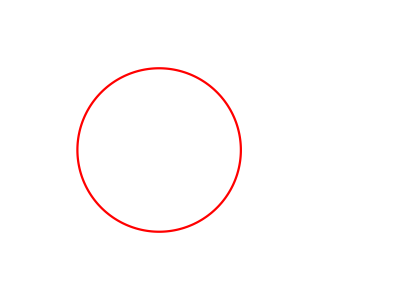

```mathematica
FF[x_,y_]:=x^2+y^2-1;
aaa=ParametricPlot[{Cos[x],Sin[x]},{x,0,2π},PlotStyle->Red,PlotRange->{{-1.5,2.5},{-1.5,1.5}},Axes->False]
```

#### Forces

```mathematica
(*RayForce[Rays_,F_,n1_,n2_]:=Module[{ForceRays,i,j,Cosθ,PoweR,Cosθt,Force,Forces,c,TheRays,na,nb,Intersect,AllForces,normal},
Forces={};
AllForces={};
TheRays=Table[1,{i,1,Length[Rays]}];
c=1;
For[i=1,i<=Length[Rays],i++,
ForceRays={};
If[Rays[[i,1]]>0&&TheRays[[i]]≠0,

Intersect=Rays[[i,2]];
normal=Normalize[{Derivative[1,0][F][Intersect[[1]],Intersect[[2]]],Derivative[0,1][F][Intersect[[1]],Intersect[[2]]]}];

AppendTo[ForceRays,Rays[[i]]];
AppendTo[AllForces,Rays[[i]]];

If[i!=Length[Rays],
If[Rays[[i+1,2]]==Intersect,
AppendTo[ForceRays,Rays[[i+1]]];
AppendTo[AllForces,Rays[[i+1]]];
TheRays[[i+1]]=0;
];
];
If[ForceRays[[1,5]],
normal=-normal;
];
Cosθ=normal.ForceRays[[1,3]];

If[ForceRays[[1,5]],
na=n2;
nb=n1,
na=n1;
nb=n2;
];
If[Length[ForceRays]==2,
Cosθt=√(1-(na/nb)^2(1-Cosθ^2));
PoweR=ForceRays[[1,4]]+ForceRays[[2,4]],
Cosθt=0;
PoweR=ForceRays[[1,4]];
AppendTo[ForceRays,{1,1,1,0}];
];
Force=PoweR/c((1-R[ForceRays[[1]],-normal,na,nb])*nb*Cosθt-na*Cosθ*(1+R[ForceRays[[1]],-normal,na,nb]))*normal;

AppendTo[Forces,{Force,Intersect}];
];
];
Return[Forces];
]; *)
ForceTrace[Rays_,F_,n1_,n2_,InteractionLimit_]:=Module[{Forces,newRays,intersects,i,intnum,TheRays,Intersect,normal,Cosθ,na,nb,Cosθt,Force,PoweR,c},

Forces={};
newRays=RayTrace[Rays,F,n1,n2,InteractionLimit];
intnum=0;
While[intnum≤InteractionLimit,
TheRays=RaySort[newRays,intnum];
intersects=Propogate[TheRays,F];
For[i=1,i≤Length[RaySort[newRays,intnum]],i++,
TheRays=RaySort[newRays,intnum];
Intersect=intersects[[i]];
PoweR=TheRays[[i,4]];
c=1;

normal=Normalize[{Derivative[1,0][F][Intersect[[1]],Intersect[[2]]],Derivative[0,1][F][Intersect[[1]],Intersect[[2]]]}];

Cosθ=-TheRays[[i,3]].normal;
If[Cosθ<0,
normal=-normal;
Cosθ=-Cosθ;
];

If[TheRays[[i,5]],
na=n2;
nb=n1,
na=n1;
nb=n2;
];
If[na>nb&&ArcCos[Cosθ]>=ArcSin[n1/n2],
Cosθt=0,
Cosθt=√(1-(na/nb)^2(1-Cosθ^2));
];
Force=PoweR/c(nb*Cosθt(1-R[TheRays[[i]],normal,na,nb])-na*Cosθ(1+R[TheRays[[i]],normal,na,nb]))*normal;
AppendTo[Forces,{Force,Intersect}];
];
intnum=intnum+1;
];
Return[Forces];
];

RayTorque[ForceList_,CoM_]:=Module[{Force,Torque,r},
r=Table[Append[ForceList[[i,2]]-CoM,0],{i,1,Length[ForceList]}];
Force=Sum[ForceList[[i,1]],{i,1,Length[ForceList]}];
Torque=Sum[Cross[r[[i]],Append[ForceList[[i,1]],0]],{i,1,Length[ForceList]}];
Return[{Force,Torque[[3]]}];
];
```

```mathematica
ForceDiagram[rays_,F_,n1_,n2_,intlimit_,com_]:=Module[{force,FForce,theforce,Rayz},
force=RayTorque[ForceTrace[rays,F,n1,n2,intlimit],com];
Rayz=RayTrace[rays,F,n1,n2,intlimit];
theforce=Normalize[force[[1]]];
FForce=√(force[[1,1]]^2+force[[1,2]]^2);
Return[Show[RayDiagram[Rayz,F],Graphics[Arrow[{{1.5,1.5},{1.5+theforce[[1]],1.5+theforce[[2]]}}]],Graphics[Text[FForce,{1.5,1.4}]]]];
];
```

```mathematica
LiftUndDrag[Forces_,α_]:=Module[{retforce},
retforce=RotationMatrix[α].Forces[[1]];
Return[retforce];
];
```

```mathematica
ArcCos[1.2]
```

0.+0.622363 ⅈ

#### Test

```mathematica
A[α_,n_]:=Raypositions[n,1.95,2,α];
b=Raypositions[4,1.95,1.2,0];
```

```mathematica
bb={{0,{-2,.975},{1,0},1,False}};
```

```mathematica
P[α_,n_,nn_]:=RayTrace[A[α,nn],FF,1,1.5,n];
```

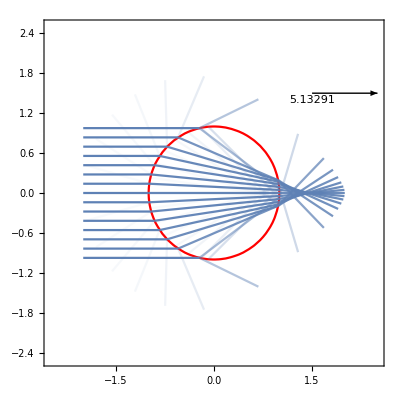

```mathematica
ForceDiagram[A[0,15],FF,1,1.5,2,{0,0}]
```

#### MultiFunction

```mathematica
MultiStop[Raylist_,F_,P_]:=Module[{p,xdir,ydir,ypos,xpos,xprop,yprop,StopF,StopP,FF,PP,intersect,i,Intersection},
xdir=Table[Raylist[[i,3,1]],{i,1,Length[Raylist]}];
ydir=Table[Raylist[[i,3,2]],{i,1,Length[Raylist]}];

xpos=Table[Raylist[[i,2,1]],{i,1,Length[Raylist]}];
ypos=Table[Raylist[[i,2,2]],{i,1,Length[Raylist]}];

xprop[x_]:=Table[xpos[[i]]+xdir[[i]]*x,{i,1,Length[Raylist]}];
yprop[x_]:=Table[ypos[[i]]+ydir[[i]]*x,{i,1,Length[Raylist]}];
StopF=Sstop[Raylist,F];
StopP=Sstop[Raylist,P];

FF[x_]:=Table[F[xprop[x][[i]],yprop[x][[i]]],{i,1,Length[Raylist]}];
PP[x_]:=Table[P[xprop[x][[i]],yprop[x][[i]]],{i,1,Length[Raylist]}];

intersect=Table[0,{i,1,Length[Raylist]}];

For[i=1,i≤Length[Raylist],i++,
If[StopF[[i]]<StopP[[i]]||StopP[[i]]==Null,
p[x_]:=FF[x][[i]];
intersect[[i]]=RootFind[p];
];
If[StopF[[i]]>StopP[[i]],
p[x_]:=PP[x][[i]];
intersect[[i]]=RootFind[p];
];
];

Return[intersect];
];
```

```mathematica
MultiProp[Raylist_,F_,P_]:=Module[{p,xdir,ydir,ypos,xpos,xprop,yprop,StopF,StopP,FF,PP,intersect,i,Intersection},
xdir=Table[Raylist[[i,3,1]],{i,1,Length[Raylist]}];
ydir=Table[Raylist[[i,3,2]],{i,1,Length[Raylist]}];

xpos=Table[Raylist[[i,2,1]],{i,1,Length[Raylist]}];
ypos=Table[Raylist[[i,2,2]],{i,1,Length[Raylist]}];

xprop[x_]:=Table[xpos[[i]]+xdir[[i]]*x,{i,1,Length[Raylist]}];
yprop[x_]:=Table[ypos[[i]]+ydir[[i]]*x,{i,1,Length[Raylist]}];
StopF=Sstop[Raylist,F];
StopP=Sstop[Raylist,P];

FF[x_]:=Table[F[xprop[x][[i]],yprop[x][[i]]],{i,1,Length[Raylist]}];
PP[x_]:=Table[P[xprop[x][[i]],yprop[x][[i]]],{i,1,Length[Raylist]}];

intersect=Table[0,{i,1,Length[Raylist]}];

For[i=1,i≤Length[Raylist],i++,
If[StopF[[i]]<StopP[[i]]||StopP[[i]]==Null,
p[x_]:=FF[x][[i]];
intersect[[i]]=RootFind[p];
];
If[StopF[[i]]>StopP[[i]],
p[x_]:=PP[x][[i]];
intersect[[i]]=RootFind[p];
];
];
Intersection=Table[{xprop[intersect[[i]]][[i]],yprop[intersect[[i]]][[i]]},{i,1,Length[intersect]}];

Return[Intersection];
];
```

```mathematica
Normallist[Raylist_,Intersects_,F_,P_]:=Module[{i,list},
list=Table[0,{i,1,Length[Intersects]}];
For[i=1,i≤Length[list],i++,
If[Abs[F[Intersects[[i,1]],Intersects[[i,2]]]]<.01,

list[[i]]=Normalize[{Derivative[1,0][F][Intersects[[i,1]],Intersects[[i,2]]],Derivative[0,1][F][Intersects[[i,1]],Intersects[[i,2]]]}],

list[[i]]=Normalize[{Derivative[1,0][P][Intersects[[i,1]],Intersects[[i,2]]],Derivative[0,1][P][Intersects[[i,1]],Intersects[[i,2]]]}];
];
];
For[i=1,i≤Length[Intersects],i++,
If[-list[[i]].Raylist[[i,3]]<0,
list[[i]]=-list[[i]];
];
];
Return[list];
];
```

```mathematica
MultiRefract[Rayss_,F_,P_,n1_,n2_]:=Module[{i,a,b,TransmissionVector,Intersects,ActualRays,NewRays,Normals,na,nb,},
NewRays=Rays[Length[Rayss]];
Intersects=MultiProp[Rayss,F,P];
(* New rays start at intersect of previous rays *)
Normals=Normallist[Rayss,Intersects,F,P];
For[i=1,i≤Length[NewRays],i++,
NewRays[[i,2]]=Intersects[[i]];
NewRays[[i,1]]=Rayss[[i,1]]+1;
];
For[i=1,i≤Length[Intersects],i++,

If[Rayss[[i,5]],
Normals[[i]]=-Normals[[i]];
na=n2;
nb=n1,
na=n1;
nb=n2;
];
b=-Normals[[i]].Rayss[[i,3]];
If[b<0,
Normals[[i]]=-Normals[[i]];
];
b=-Normals[[i]].Rayss[[i,3]];
a=(na/nb)^2(1-b^2);
TransmissionVector=na/nb Rayss[[i,3]]+(na/nb b-√(1-a))*Normals[[i]];
NewRays[[i,4]]=(1-R[Rayss[[i]],Normals[[i]],na,nb])*Rayss[[i,4]];
NewRays[[i,3]]=TransmissionVector;
NewRays[[i,5]]=!Rayss[[i,5]];
];
ActualRays={};
For[i=1,i≤Length[NewRays],i++,
If[NewRays[[i,4]]==0,
Continue,
AppendTo[ActualRays,NewRays[[i]]];
];
];
Return[ActualRays];
];
```

```mathematica
MultiReflect[Rayss_,F_,P_,n1_,n2_]:=Module[{ReflRays,Intersects,Normals,i,θc,b,na,nb},
ReflRays=Rays[Length[Rayss]];
Intersects=MultiProp[Rayss,F,P];
Normals=Normallist[Rayss,Intersects,F,P];
For[i=1,i≤Length[Rayss],i++,
ReflRays[[i,2]]=Intersects[[i]];
ReflRays[[i,1]]=Rayss[[i,1]]+1;
b=-Normals[[i]].Rayss[[i,3]];
If[Rayss[[i,5]],
na=n2;
nb=n1,
na=n1;
nb=n2;
];
ReflRays[[i,3]]=Rayss[[i,3]]+2(b)*Normals[[i]];
ReflRays[[i,5]]=Rayss[[i,5]];
ReflRays[[i,4]]=R[Rayss[[i]],Normals[[i]],na,nb]*Rayss[[i,4]];
];
Return[ReflRays];
];
```

```mathematica
MultiRayInteraction[Rays_,F_,P_,n1_,n2_]:=Module[{Intersects,Normals,ReflectRay,RefractRay,EndRays},
Intersects=MultiProp[Rays,F,P];
ReflectRay=MultiReflect[Rays,F,P,n1,n2];
RefractRay=MultiRefract[Rays,F,P,n1,n2];
EndRays=Join[Rays,ReflectRay,RefractRay];
Return[EndRays];
];
```

```mathematica
MultiTrace[Rays_,F_,P_,n1_,n2_,InteractionLimit_]:=Module[{TheRays,a,NewRay,p,nin,nout,RefRays,i,s1,pp,InteractionNumber,TotalRays,refrays},
InteractionNumber=1;
TotalRays=Rays;
p=MultiRayInteraction[Rays,F,P,n1,n2];
pp=RaySort[p,InteractionNumber];
While[InteractionNumber≤InteractionLimit,
InteractionNumber=InteractionNumber+1;
TotalRays=Union[TotalRays,p];
p=MultiRayInteraction[pp,F,P,n1,n2];
pp=RaySort[p,InteractionNumber];
];
Return[TotalRays];
];
```

```mathematica
MultiDiagram[Rays_,F_,P_]:=Module[{plots,i,stops,Q},
plots=Table[0,{i,0,Length[Rays]}];
Q[x_,y_]:=Piecewise[{{x^2+y^2-1,x<0}},x];
plots[[1]]=ContourPlot[Q[x,y]==0,{x,-2.5,2.5},{y,-2.5,2.5},ContourStyle->Red,Exclusions->None,Axes->False,Frame->False];
stops=MultiStop[Rays,F,P];
For[i=1,i≤Length[stops],i++,
If[stops[[i]]==0||stops[[i]]==Null,
stops[[i]]=1;
];];
For[i=1,i≤Length[Rays],i++,
If[Rays[[i,5]]||Rays[[i,1]]==0,

plots[[i+1]]=ParametricPlot[{Rays[[i,2,1]]+Rays[[i,3,1]]*s,Rays[[i,2,2]]+Rays[[i,3,2]]*s},{s,0,stops[[i]]},PlotStyle->Opacity[Rays[[i,4]]],Axes->False],

plots[[i+1]]=ParametricPlot[{Rays[[i,2,1]]+Rays[[i,3,1]]*s,Rays[[i,2,2]]+Rays[[i,3,2]]*s},{s,0,1},PlotStyle->Opacity[Rays[[i,4]]],Axes->False];
];
];
Return[Show[plots]];
];
```

```mathematica
MultiForceTrace[Rays_,F_,P_,n1_,n2_,InteractionLimit_]:=Module[{Forces,newRays,intersects,i,intnum,TheRays,Intersect,normal,normals,Cosθ,na,nb,Cosθt,Force,PoweR,c},

Forces={};
newRays=MultiTrace[Rays,F,P,n1,n2,InteractionLimit];
intnum=0;
While[intnum≤InteractionLimit,
TheRays=RaySort[newRays,intnum];
intersects=MultiProp[TheRays,F,P];
normals=Normallist[TheRays,intersects,F,P];
For[i=1,i≤Length[RaySort[newRays,intnum]],i++,
TheRays=RaySort[newRays,intnum];
Intersect=intersects[[i]];
PoweR=TheRays[[i,4]];
c=1;
normal=normals[[i]];


Cosθ=-TheRays[[i,3]].normal;
If[Cosθ<0,
normal=-normal;
Cosθ=-Cosθ;
];

If[TheRays[[i,5]],
na=n2;
nb=n1,
na=n1;
nb=n2;
];
If[na>nb&&ArcCos[Cosθ]>=ArcSin[n1/n2],
Cosθt=0,
Cosθt=√(1-(na/nb)^2(1-Cosθ^2));
];
Force=PoweR/c(nb*Cosθt(1-R[TheRays[[i]],normal,na,nb])-na*Cosθ(1+R[TheRays[[i]],normal,na,nb]))*normal;
AppendTo[Forces,{Force,Intersect}];
];
intnum=intnum+1;
];
Return[Forces];
];
```

```mathematica
MultiForceMultiDiagram[Rays_,F_,P_,n1_,n2_,intlimit_,com_]:=Module[{Rayz,force,theforce,FForce},
force=RayTorque[MultiForceTrace[Rays,F,P,n1,n2,intlimit],com];
Rayz=MultiTrace[Rays,F,P,n1,n2,intlimit];
theforce=Normalize[force[[1]]];
FForce=√(force[[1,1]]^2+force[[1,2]]^2);
Return[Show[MultiDiagram[Rayz,F,P],Graphics[Arrow[{{1,2},{1+theforce[[1]],2+theforce[[2]]}}]],Graphics[Text[FForce,{1,1.8}]],Graphics[Text[force[[2]],{2,-2}]],Graphics[Text["τ =",{1.5,-2}]],Graphics[Text["ẑ",{2.4,-2}]]]];
];
MultiShoot[n_,α_,F_,P_]:=Module[{Raylist,Vector,xdir,ydir,PP,Δx,tot,xpos,ypos,k,j,Firsthit,Endhit,xprop,yprop,FF,intersect,i,p},
Raylist=Raypositions[n,3,2,α];
Vector=Normalize[{-2 Cos[α],-2 Sin[α]}-{-2 Cos[α]-Sin[α],-2 Sin[α]+Cos[α]}];
xdir=Table[Raylist[[i,3,1]],{i,1,Length[Raylist]}];
ydir=Table[Raylist[[i,3,2]],{i,1,Length[Raylist]}];
xpos=Table[Raylist[[i,2,1]],{i,1,Length[Raylist]}];
ypos=Table[Raylist[[i,2,2]],{i,1,Length[Raylist]}];
xprop[x_]:=Table[xpos[[i]]+xdir[[i]]*x,{i,1,Length[Raylist]}];
yprop[x_]:=Table[ypos[[i]]+ydir[[i]]*x,{i,1,Length[Raylist]}];
FF[x_]:=Table[F[xprop[x][[i]],yprop[x][[i]]],{i,1,Length[Raylist]}];
intersect=Table[0,{i,1,Length[Raylist]}];
PP[x_]:=Table[P[xprop[x][[i]],yprop[x][[i]]],{i,1,Length[Raylist]}];
For[i=1,i≤Length[Raylist],i++,
p[x_]:=FF[x][[i]];
intersect[[i]]=BisectWhile[p,-5,3,10^-4];
If[intersect[[i]]==0,
p[x_]:=PP[x][[i]];
intersect[[i]]=BisectWhile[p,-5,3,10^-4];
];
];
j=1;
k=n;
While[intersect[[j]]==0,
j=j+1;
];
While[intersect[[k]]==0,
k=k-1;
];
Firsthit=Raylist[[j,2]];
If[α≤π/2,
Firsthit=Firsthit;
];
Endhit=Raylist[[k,2]];
If[α≥3π/2,
Endhit=Endhit;
];
tot=Firsthit-Endhit;
Δx=(√(tot[[1]]^2+tot[[2]]^2))/(n-1);
For[i=0,i<n,i++,
Raylist[[i+1,2]]=Firsthit-i*Δx*Vector;
];
Return[Raylist];
];
```

#### Tests

```mathematica
F[x_,y_]:=Piecewise[{{x^2+y^2-1,x<0},{x^2+y^2-16,x>=0}}];
P[x_,y_]:=Piecewise[{{x,x>-1&&y^2<=1}},x+5];
```

```mathematica
b=Raypositions[25,1.5,1.5,π/6];
bb=Raypositions[25,1.5,1.5,π];
bbb=Raypositions[25,1.5,1.5,0];
```

```mathematica
c[n_,l_,α_]:=Raypositions[n,l,2,α];
```

```mathematica
MultiForceMultiDiagram[d[35,1.6,π/6],F,P,1,1.5,3,{-4/(3π),0}]
```

Part::partd: Part specification d[35,1.6,π/6]⟦1,3,1⟧ is longer than depth of object.

Part::partd: Part specification d[35,1.6,π/6]⟦2,3,1⟧ is longer than depth of object.

Part::partw: Part 3 of π/6 does not exist.

Part::partd: Part specification d[35,1.6,π/6]⟦1,3,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 3 of π/6 does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Join::heads: Heads d and List at positions 1 and 2 are expected to be the same.

Union::heads: Heads Join and d at positions 2 and 1 are expected to be the same.

General::stop: Further output of Union::heads will be suppressed during this calculation.

$Aborted

```mathematica
d[n_,α_]:=RayShooting2[n,α];
dd[n_,α_]:=RayShooting3[n,α];
```

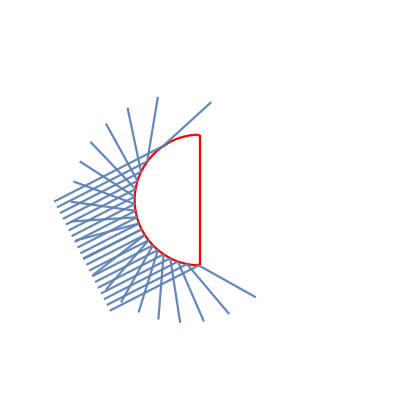

```mathematica
int3=Rotate[MultiDiagram[MultiTrace[dd[20,3π/20],F,P,1,100000,1],F,P],-3π/20]
```

#### one interaction, 50 rays, π/40 intervals, n=1.25

```mathematica
J=Table[MultiForceTrace[dd[35,i π/40],F,P,1,1.25,1],{i,1,80}]
```

{{{{-0.0422264,0.188955},{-0.218094,0.975928}},{{-0.12387,0.256585},{-0.434752,0.90055}},67,{{0.213394,0.},{0.,-0.942388}}},{1},76,{1},{1}}
 |  |  |  |

```mathematica
J={{{{{{-0.04222643396501595,0.1889553728105997},{-0.21809357834251109,0.9759278616197812}},{{-0.12386969953824752,0.2565851229339144},{-0.43475196772226465,0.900550235445874}},67,{{0.21339357889440663,0.},{0.,-0.9423876531559457}}},{1},76,{1},{1}}}, {{{, , , , }}}};
```

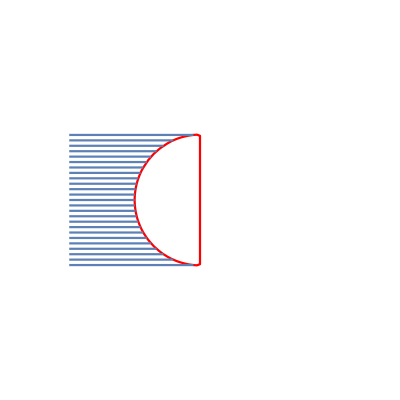
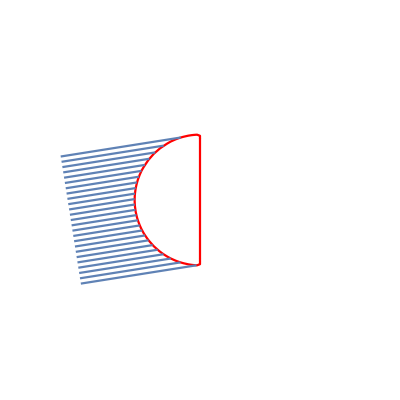
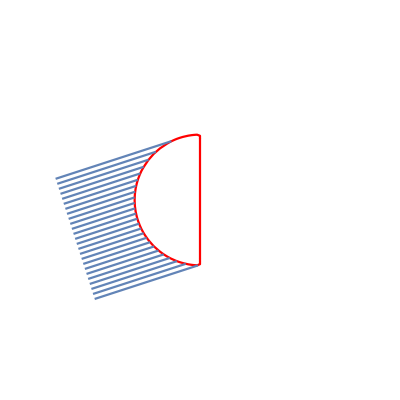
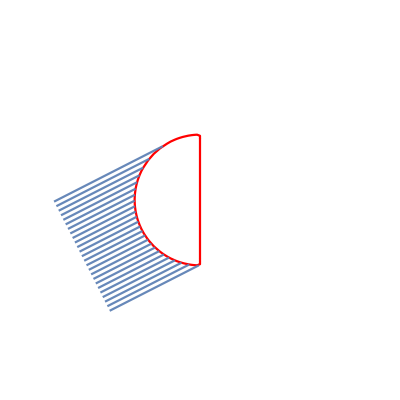
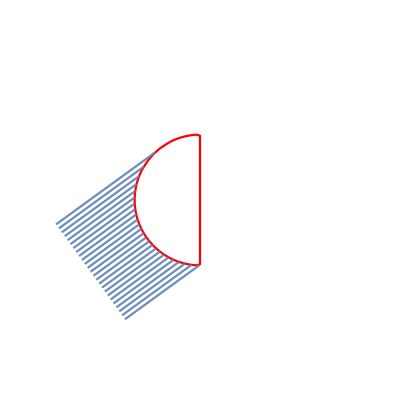
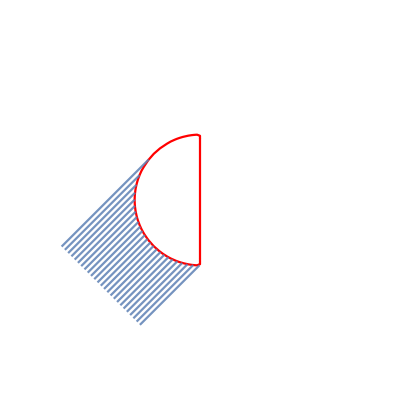
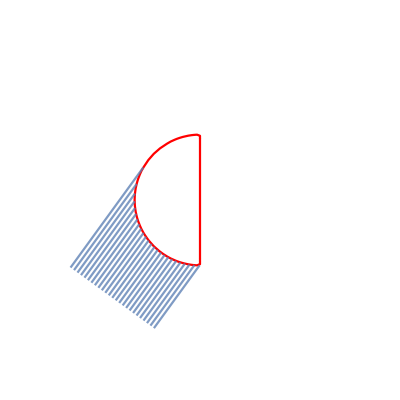
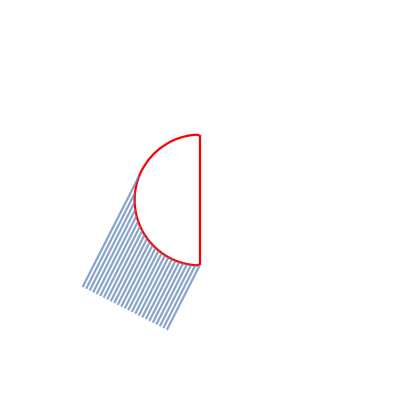

```mathematica
Table[MultiDiagram[d[25,i π/20],F,P],{i,0,39}]
```

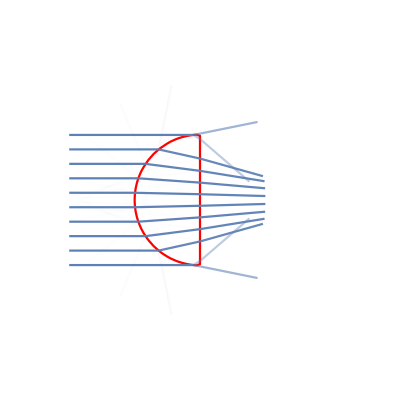
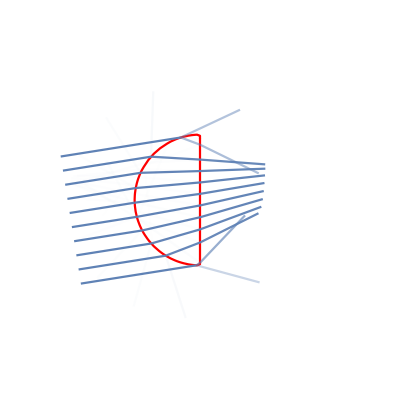
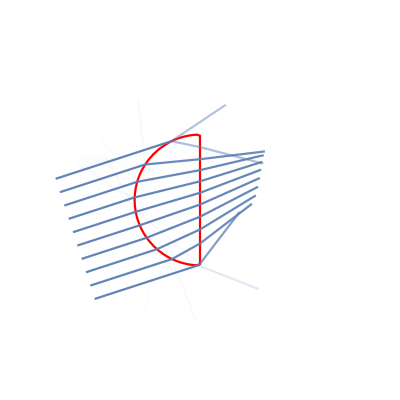
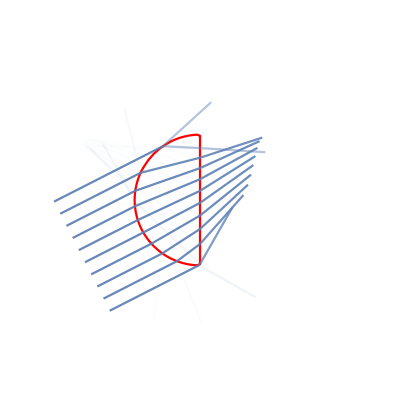
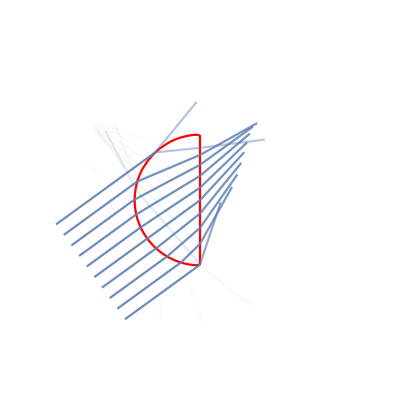
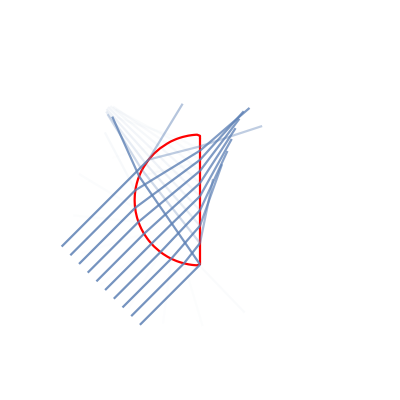
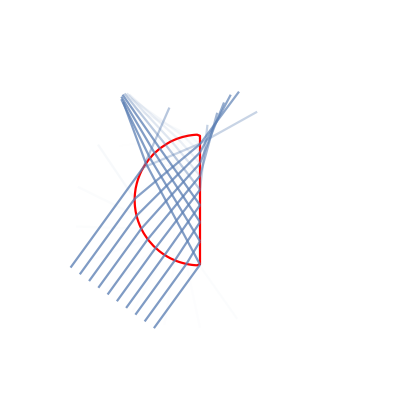
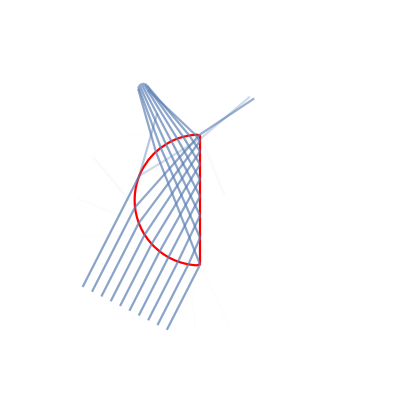

```mathematica
Table[Rotate[MultiDiagram[MultiTrace[d[10,i π/20],F,P,1,1.25,3],F,P],-i π/20],{i,0,39}]
```